FittedModel[0.207394-4.31429×10^-6 x]

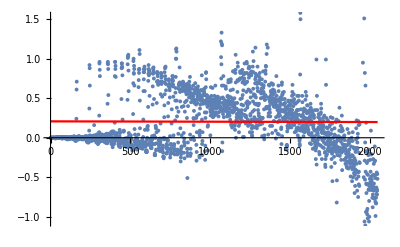

0.131829

{4.712×10^-19,0.824746}

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "intersect-fixed"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x,{a,b},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
nlm["ParameterPValues"]
```